# Lesson 7: Derivatives and Rates of Change

## Overview

```mathematica
f[x_]:=8 x^4-8Sin[x]+5/x
```

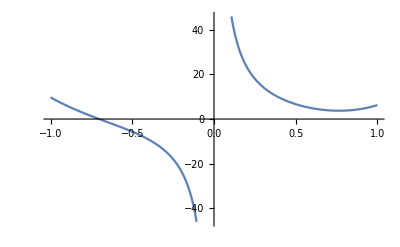

```mathematica
Plot[f[x],{x,-1,1}]
```

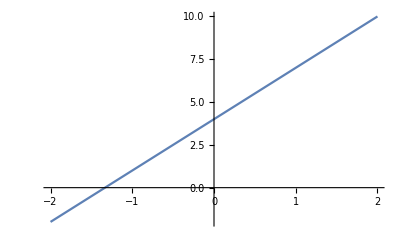

```mathematica
Plot[3x+4,{x,-2,2}]
```

## Notion of a derivative

```mathematica
f[x_]:=1/x
```

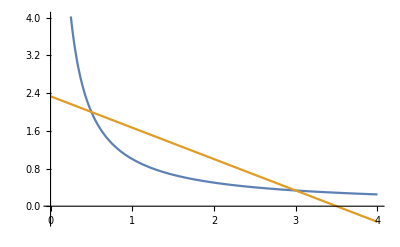

```mathematica
Plot[{f[x],1/3-2/3(x-3)},{x,0,4}]
```

## Tangent Line of a Polynomial

```mathematica
f[x_]:=x^3
```

```mathematica
m = Limit[(f[x]-f[1])/(x-1),x->1]
```

3

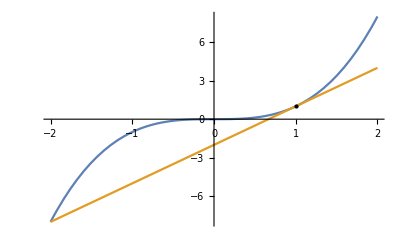

```mathematica
Plot[{f[x],m(x-1)+f[1]},{x,-2,2},
Epilog->{PointSize[Large],Black, Point[{1,f[1]}]}]
```

```mathematica
f[x_]:=1/x
Grid[{{y-1==m (x-1)},{y==m x+2}},Alignment->Right]//TraditionalForm
```

y-1==1-x
y==2-x

```mathematica
m= Limit[DifferenceQuotient[f[x],{x,h}],h->0]/.x->1
```

-1

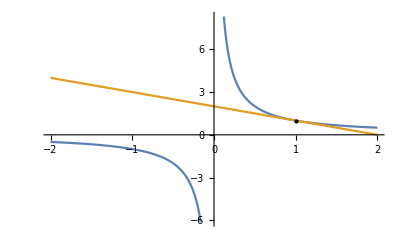

```mathematica
Plot[{f[x],m x+2},{x,-2,2},Epilog->{PointSize[Large],Black,Point[{1,f[1]}]}]
```

## Velocity

```mathematica
s[t_]:=5t
```

Instantaneous velocity is given by the limit of the difference quotient:

```mathematica
v[t_]:=Limit[DifferenceQuotient[s[x],{x,h}],h->0]/.x->t
```

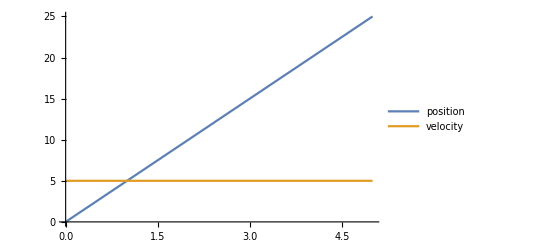

```mathematica
Plot[{s[t],v[t]},{t,0,5}, PlotLegends->{"position","velocity"}]
```

## Physics Problem

```mathematica
s[t_]:=100-4.9 t^2;
```

```mathematica
Limit[DifferenceQuotient[s[t],{t,h}],h->0]/.t->2
```

-19.6

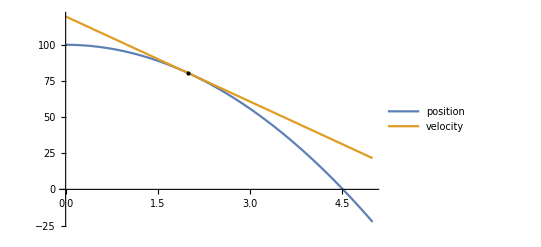

```mathematica
Plot[{s[t], -19.6 (t - 2) + s[2]}, {t, 0, 5}, Sequence[Epilog -> {
PointSize[Large], Black, 
Point[{2, 
s[2]}]}, PlotLegends -> {"position", "velocity"}]]
```

```mathematica
sol=Solve[{s[t]==0,t>0},t]
```

{{t→4.51754}}

```mathematica
Limit[DifferenceQuotient[s[t],{t,h}],h->0]/.t->sol[[1,1,2]]
```

-44.2719

## Derivatives at Points

```mathematica
f[x_]:=x^3
f'[1]
```

3

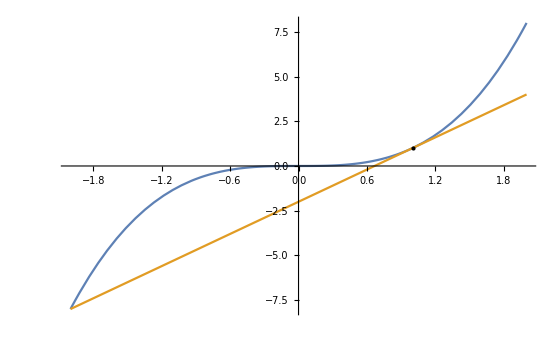

```mathematica
Plot[{f[x],f'[1](x-1)+f[1]},{x,-2,2},
Epilog->{PointSize[Large],Black,Point[{1,f[1]}]}]
```

## Tangent Line of a Parabola

```mathematica
f[x_]:=2 x^2+3x-10
```

```mathematica
tangent[x_]:=f'[2](x-2)+f[2]
```

```mathematica
tangent[x]//Simplify
```

-18+11 x

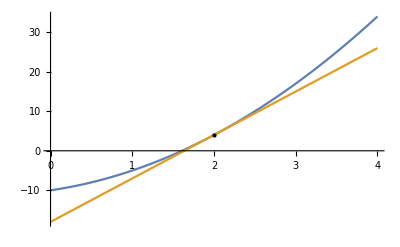

```mathematica
Plot[{f[x],tangent[x]},{x,0,4},
Epilog->{PointSize[Large],Black, Point[{2,f[2]}]}]
```

## Average Rate of Change

Average rate of change for x^2 in closed interval [-0.5,0.25].

```mathematica
avg = ((.25)^2-(-.5)^2)/(.25-(-.5))
```

-0.25

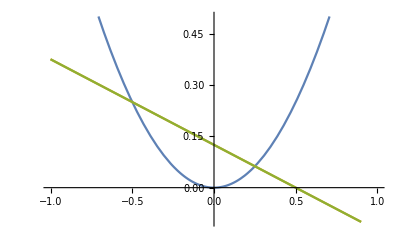

```mathematica
Plot[{x^2,(-.5)^2+avg(x+0.5),(.25)^2+avg(x-0.25)},{x,-1,1},PlotRange->{-.1,.5}]
```

## Instantaneous Rate of Change

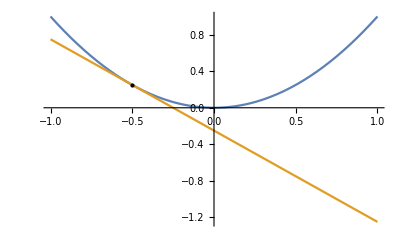

```mathematica
Plot[{x^2,(-.5)^2+Limit[(h^2-(-.5)^2)/(h-(-.5)), h->-.5](x+.5)},
{x,-1,1},Epilog->{Black,PointSize[Large],Point[{-.5,.25}]}]
```

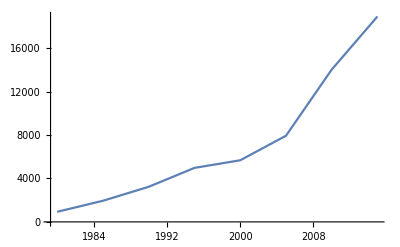

```mathematica
ListLinePlot[{{1980,930.2},{1985,1945.9},{1990,3233.3},{1995,4974.},{2000,5674.2},{2005,7932.7},{2010,14030},{2015,18920}}]
```

1

1.69761×10^12 $

EntityValue::nodat: Unable to download data. Some or all results may be missing.

Missing[RetrievalFailure]

```mathematica
debtdata[x_]=Piecewise[{{930.2,x==1980},{1945.9,x==1985},{3233.3,x==1990},{4974.0,x==1995},{5674.2,x==2000},{7932.7,x==2005},{14030,x==2010},{18920,x==2015}},Undefined];
```

```mathematica
debtDerivative[x_]:=(debtdata[x]-debtdata[2010])/(x-2010)
```

```mathematica
(debtDerivative[2005]+debtDerivative[2015])/2
```

1098.73